# C. Sun Spectrum Calculation (Energy vs Spectral Density)

## Constants and Cases

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.511*10^6; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*CBETA 150 MeV 0.5% Bandwidth Case*)
CBETA150={Ee->150*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.435*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.126976,σL->25*10^-6,ΔEe->5*10^-4,L->10,npts->100};
CBETA114={Ee->114*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.572*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.096,σL->25*10^-6,ΔEe->5*10^-4,L->10,npts->100};
CBETA078={Ee->78*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.836*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.066,σL->25*10^-6,ΔEe->5*10^-4,L->10,npts->100};
CBETA042={Ee->42*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->1.551*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.035,σL->25*10^-6,ΔEe->5*10^-4,L->10,npts->100};

overfocusCBETA={Ee->150*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.435*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.01,σL->25*10^-6,ΔEe->5*10^-4,L->10,npts->100};
underfocusCBETA={Ee->150*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.435*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->1,σL->25*10^-6,ΔEe->5*10^-4,L->10,npts->100};
matchCBETA={Ee->150*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.435*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.611,σL->25*10^-6,ΔEe->5*10^-4,L->10,npts->100};
```

```mathematica
(*C. Sun Fig.3 Cases*)
CSUNBLACK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(14/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
CSUNRED={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(12/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
CSUNBLUE={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(10/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
CSUNPINK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(8/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
CSUNGREEN={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(4/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
```

The cases shown are the CBETA ICS at 150MeV for the 0.5% bandwidth case and all the cases from Fig. 3 C. Sun et al PRSTAB 12, 062801 (2009). Emittance normalised, SI units used. npts is the no.points for the tables (changes between MeV and keV range).
Unknowns for the C. Sun cases are: Q, Epulse, βx, σL - the quantities of electrons and photons and the size of the bunch/pulse at the IP.

```mathematica
(*C. Sun Fig. 4a Emittance Cases with Storage Ring β^* i.e ~m scale*)
```

```mathematica
emitBLACK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6*10,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
emitRED={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6*200,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
emitBLUE={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6*2000,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
emitPINK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6*10000,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
```

```mathematica
(*C. Sun Fig 4b Energy Spread Cases*)
```

```mathematica
ΔEeBLACK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->5*10^-4,L->60,npts->10000};
ΔEeRED={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
ΔEeBLUE={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->4*10^-3,L->60,npts->10000};
ΔEePINK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->8*10^-3,L->60,npts->10000};
```

```mathematica
(*Cases of varying Subscript[σ, L] and β^*, use Fig.3 Blue as a base*)
```

```mathematica
β001σL07={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(10/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->0.01,σL->0.707*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
β01σL7={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(10/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->0.1,σL->7.1*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
β1σL22={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(10/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
β2σL31={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(10/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->2,σL->31.6*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
β10σL70={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(10/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->10,σL->70.1*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
```

```mathematica
(*Storage Ring vs Linac Comparison*)
```

```mathematica
LinacBLACK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6*10,βx->0.1,σL->7.1*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
SRBLACK={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(16/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6*10,βx->1.0,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
```

```mathematica
(*Collimator Shape Case*)
```

```mathematica
ColShape={Ee->500*10^6,Q->1.5*10^-9,Epulse->1,λ->800*10^-9,θcol->(12/60)*10^-3,ϕ->0,ϵnx->0.0489*10^-6,βx->1,σL->22.4*10^-6,ΔEe->2*10^-3,L->60,npts->10000};
```

```mathematica
trialcase=matchCBETA;
```

## Observation Angle

```mathematica
θob[θx_,yc_,L_]:=Sqrt[θx^2+(yc/L)^2];
```

## SPE Intermediaries

```mathematica
(*Intermediary calculations for the scattered photon energy*)
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
```

## Scattered Photon Energy Calc

```mathematica
Eγset[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
(*use 3 sigma of ΔEe to get 'head tail' as the compton edge is not sharp when you have an electron beam energy spread*)
```

```mathematica
Eγset[λ,Ee,ϕ,0]/.trialcase
```

400553.

## CSUN Preliminaries + Collimation

```mathematica
(*Preliminaries*)
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(EL[λ]*elecharge);
ϵx[Ee_,ϵnx_]:=ϵnx/(β[Ee]*γ[Ee]);
k[λ_]:=EL[λ]/(hbar*clight);
zr[λ_,σL_]:=(π*σL^2)/λ;
σe[ΔEe_,Ee_]:=ΔEe*Ee; (*Conversion from relative*)
```

```mathematica
(*Collimation*)
R[L_,θcol_]:=L*θcol;
x0[L_,θcol_]:=R[L,θcol];(*Condition for circular collimator*) 
y0[L_,θcol_,xc_]:=Re[Sqrt[R[L,θcol]^2-xc^2]];
```

Square aperture created in two dimensions (x_0= a for x_c, y_0=b for x_c), Circular aperture based on the radius (x_0=R for x_c, y_0= Re Sqrt[R^2 - x_c^2] for y_c or vice versa depending on order of integration).

```mathematica
ϵx[Ee,ϵnx]/.trialcase
```

1.02201×10^-9

## CSUN Intermediaries

```mathematica
a[λ_]:=EL[λ]/me;
γbar[λ_,Eγ_,θx_,yc_,L_]:=(2*Eγ*a[λ])/(4*EL[λ]-Eγ*θob[θx,yc,L]^2)*(1+Sqrt[1+(4*EL[λ]-Eγ*θob[θx,yc,L]^2)/(4*a[λ]^2*Eγ)]);
ξx[βx_,L_,λ_,Ee_,ϵnx_,σL_]:=1+(βx/L)^2+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζx[λ_,βx_,Ee_,ϵnx_,σL_]:=1+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,λ,Ee,ϵnx,σL])/(βx*ζx[λ,βx,Ee,ϵnx,σL])];
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θxmax[λ_,Eγ_,yc_,L_]:=Sqrt[(4*EL[λ])/Eγ-(yc/L)^2];
```

## Prefactor

```mathematica
(*Prefactor*)
prefactor[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_]:=(re^2*L^2*Ne[Q]*NL[Epulse,λ])/(2*π^2*hbar*clight*zr[λ,σL]*Sqrt[ζx[λ,βx,Ee,ϵnx,σL]]*σγ[ΔEe,Ee]*σθx[Ee,ϵnx,βx,L,λ,σL]);
prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]/.trialcase
```

5.45907×10^8

## Separated Integral Terms

```mathematica
(*Separated Integral Terms, Each is calculated for the maximum scattered energy value, Plot of how each term looks 0 to θcol*)
```

```mathematica
(*Term 1*)
term1[λ_,Eγ_,θx_,yc_,L_]:=(γbar[λ,Eγ,θx,yc,L]/(1+2*γbar[λ,Eγ,θx,yc,L]*a[λ]));
```

```mathematica
(*Term2*)
term2[λ_,Eγ_,θx_,yc_,L_]:=(1/4*((4*γbar[λ,Eγ,θx,yc,L]^2*EL[λ])/(Eγ*(1+γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2))+(Eγ*(1+γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2))/(4*γbar[λ,Eγ,θx,yc,L]^2*EL[λ]))-(γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2)/((1+γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2)^2));
```

```mathematica
(*Term3*)
term3[θx_,xc_,L_,Ee_,ϵnx_,βx_,λ_,σL_,yc_,ΔEe_,Eγ_]:=Exp[-(θx-xc/L)^2/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2)-(γbar[λ,Eγ,θx,yc,L]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)];
```

## Individual Term Plotting

```mathematica
(*Term1*)
```

```mathematica
INTterm1[λ_,Eγ_,L_]:=NIntegrate[term1[λ,Eγ,θx,yc,L]/.trialcase,{yc,-y0[L,θcol,xc]/.trialcase,y0[L,θcol,xc]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}];
```

```mathematica
Term1dat=Table[{Eγ,INTterm1[λ,Eγ,L]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

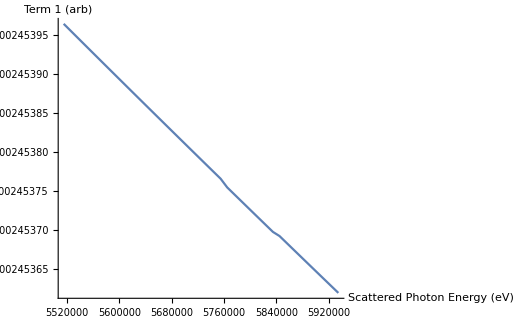

```mathematica
ListLinePlot[Term1dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 1 (arb)"}]
```

```mathematica
(*Term 2*)
```

```mathematica
INTterm2[λ_,Eγ_,L_]:=NIntegrate[term2[λ,Eγ,θx,yc,L]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}]
```

```mathematica
Term2dat=Table[{Eγ,INTterm2[λ,Eγ,L]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

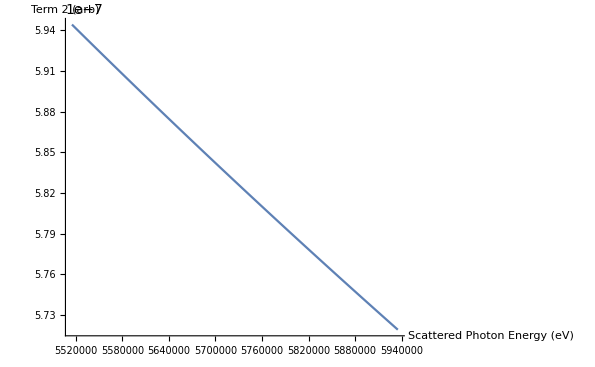

```mathematica
ListLinePlot[Term2dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 2 (arb)"}]
```

```mathematica
(*Term 3*)
```

```mathematica
INTterm3[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}]
```

```mathematica
Term3dat=Table[{Eγ,INTterm3[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.03312×10^-9 and 2.45279×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.07355×10^-9 and 2.50504×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.11496×10^-9 and 2.55499×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

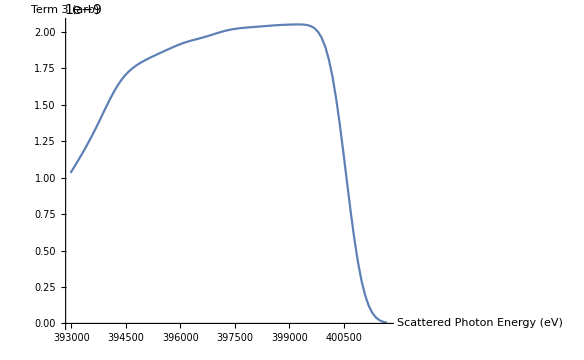

```mathematica
ListLinePlot[Term3dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 3 (arb)"}]
```

## Integration Strategies Investigation

```mathematica
(*Global Adaptive*)
```

```mathematica
INTterm3GA[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->"GlobalAdaptive"]
```

```mathematica
Term3datGA=Timing[Table[{Eγ,INTterm3GA[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Term3datGA⟦1⟧
```

111.078

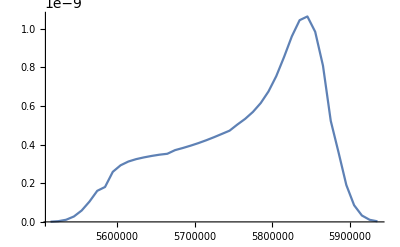

```mathematica
ListLinePlot[Term3datGA⟦2⟧]
```

```mathematica
(*Global Adaptive using Duffy's Coordinates*)
```

```mathematica
INTterm3GAD[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"GlobalAdaptive","SingularityHandler"->"DuffyCoordinates"}]
```

```mathematica
Term3datGAD=Timing[Table[{Eγ,INTterm3GAD[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Term3datGAD⟦1⟧
```

83.3594

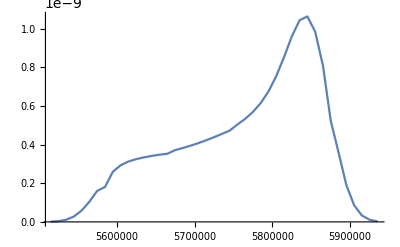

```mathematica
ListLinePlot[Term3datGAD⟦2⟧]
```

```mathematica
(*Local Adaptive*)
```

```mathematica
INTterm3LA[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->"LocalAdaptive"]
```

```mathematica
Term3datLA=Table[{Eγ,INTterm3LA[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

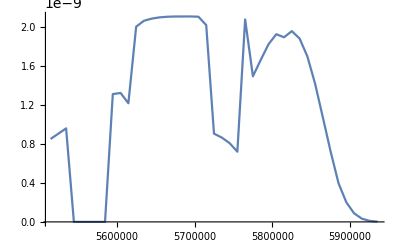

```mathematica
ListLinePlot[Term3datLA]
```

```mathematica
(*Double Exponential*)
```

```mathematica
INTterm3DE[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->"DoubleExponential"]
```

```mathematica
Term3datDE=Table[{Eγ,INTterm3DE[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at θx = 1..

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

```mathematica
ListPlot[Term3datDE]
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at θx = 1..

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

-Graphics-

```mathematica
(*Trapezoidal*)
```

```mathematica
INTterm3T[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->"Trapezoidal"]
```

```mathematica
Term3datT=Table[{Eγ,INTterm3T[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in θx in the region {{0.,1.},{0.,1.},{0.,1.}}. NIntegrate obtained 1.78043×10^-11 and 5.31977×10^-11 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in θx in the region {{0.,1.},{0.,1.},{0.,1.}}. NIntegrate obtained 6.5586×10^-11 and 1.96617×10^-10 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in θx in the region {{0.,1.},{0.,1.},{0.,1.}}. NIntegrate obtained 1.94096×10^-10 and 5.82191×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

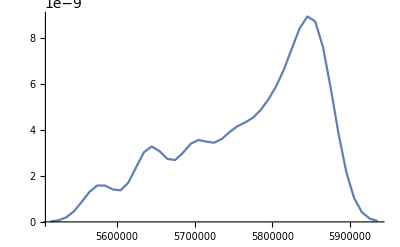

```mathematica
ListLinePlot[Term3datT]
```

```mathematica
(*Multi Periodic*)
```

```mathematica
INTterm3MP[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"MultiPeriodic",MaxPoints->500000}]
```

```mathematica
Term3datMP=Table[{Eγ,INTterm3MP[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-10*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}]//Timing;
```

NIntegrate::maxp: The integral failed to converge after 635208 integrand evaluations. NIntegrate obtained 1.58173×10^-10 and 2.17948×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 635208 integrand evaluations. NIntegrate obtained 1.92214×10^-10 and 9.33757×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 635208 integrand evaluations. NIntegrate obtained 2.28016×10^-10 and 1.51195×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
Term3datMP⟦1⟧
```

114.109

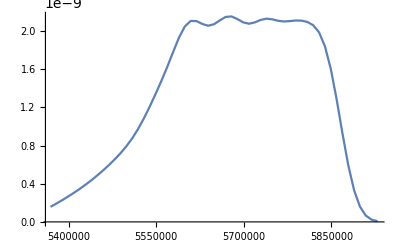

```mathematica
ListLinePlot[Term3datMP⟦2⟧]
```

```mathematica
(*Monte Carlo*)
```

```mathematica
INTterm3MC[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"MonteCarlo",MaxPoints->500000}]
```

```mathematica
Term3datMC=Table[{Eγ,INTterm3MC[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-10*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 1.3932×10^-10 and 1.48379×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 1.8479×10^-10 and 1.64571×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 2.35301×10^-10 and 1.94909×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

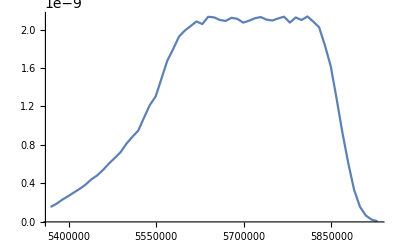

```mathematica
ListLinePlot[Term3datMC]
```

```mathematica
(*Quasi Monte Carlo*)
```

```mathematica
INTterm3QMC[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}]
```

```mathematica
Term3datQMC=Table[{Eγ,INTterm3QMC[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-10*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}]//Timing;
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.61062×10^-10 and 1.66024×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.94564×10^-10 and 1.82328×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 2.31179×10^-10 and 2.02033×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
Term3datQMC⟦1⟧
```

62.3594

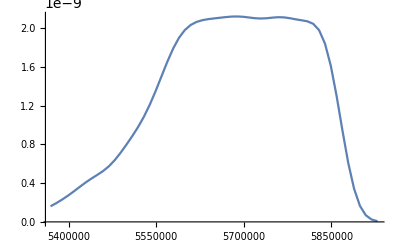

```mathematica
ListLinePlot[Term3datQMC⟦2⟧]
```

```mathematica
(* Quasi Monte Carlo with Duffy Coords*)
```

```mathematica
(*Adaptive Monte Carlo*)
```

```mathematica
INTterm3AMC[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->"AdaptiveMonteCarlo"]
```

```mathematica
Term3datAMC=Table[{Eγ,INTterm3AMC[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

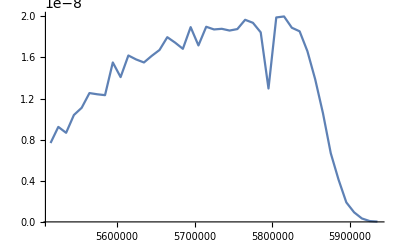

```mathematica
ListLinePlot[Term3datAMC]
```

```mathematica
(*Adaptive Quasi Monte Carlo*)
```

```mathematica
INTterm3AQMC[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->"AdaptiveQuasiMonteCarlo"]
```

```mathematica
Term3datAQMC=Table[{Eγ,INTterm3AQMC[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.63978×10^-9 and 4.67786×10^-11 for the integral and error estimates.

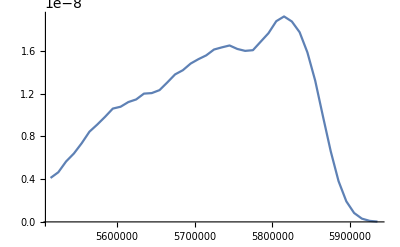

```mathematica
ListLinePlot[Term3datAQMC]
```

[CBETA ICS] Multi-Periodic and Quasi Monte Carlo integration methods seem to be improvements on currently used methods but seem to exhibit some strange tail behaviours still (unless this is compensated elsewhere). QMC runs quicker, MP looks better. Is there any way to improve these methods? 
Both Global Adaptive and Local Adaptive seem to have issues beyond 396.9 keV. 

[C SUN BLACK]  Again MP and QMC methods are good. Local and Global Adaptive methods are better in this case too.

## Integral Term

```mathematica
intterm[λ_,Ee_,θx_,yc_,L_,xc_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=term1[λ,Eγ,θx,yc,L]*term2[λ,Eγ,θx,yc,L]*term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ];
```

```mathematica
INTterm[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yc,-y0[L,θcol,xc]/.trialcase,y0[L,θcol,xc]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}];
```

## Integral Term Plotting

```mathematica
Intdat=Table[{Eγ,INTterm[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 4.04038×10^-6 and 5.65772×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 4.35757×10^-6 and 5.88446×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 4.71419×10^-6 and 6.12551×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

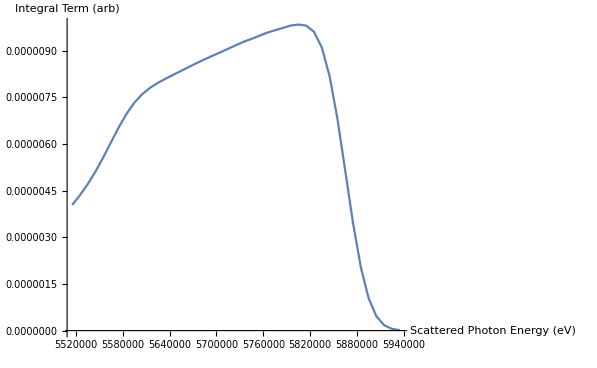

```mathematica
ListLinePlot[Intdat,AxesLabel->{"Scattered Photon Energy (eV)","Integral Term (arb)"}]
```

## Order of Integration Investigation

6 individual ways to do the orders of integration. Try and time each to see fastest method or if they produce different answers.

```mathematica
INT1term[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}];
```

```mathematica
Intdat1=Table[{Eγ,INT1term[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::nlim: θx = -√(1.12405×10^-6-yc^2/3600) is not a valid limit of integration.

NIntegrate::nlim: θx = -√(1.12202×10^-6-yc^2/3600) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
INT2term[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}];
```

```mathematica
Intdat2=Table[{Eγ,INT2term[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::nlim: θx = -√(1.12405×10^-6-yc^2/3600) is not a valid limit of integration.

NIntegrate::nlim: θx = -√(1.12202×10^-6-yc^2/3600) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
INT3term[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}];
```

```mathematica
Intdat3=Table[{Eγ,INT3term[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::nlim: θx = -√(1.12405×10^-6-yc^2/3600) is not a valid limit of integration.

NIntegrate::nlim: θx = -√(1.12202×10^-6-yc^2/3600) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
INT4term[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}];
```

```mathematica
Intdat4=Timing[Table[{Eγ,INT4term[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-10*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}]];
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 6.62157×10^-8 and 6.81764×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 8.02444×10^-8 and 7.51362×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 9.56592×10^-8 and 8.35422×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
Intdat4⟦1⟧
```

67.625

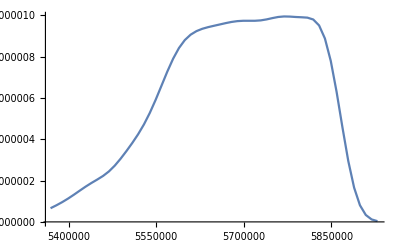

```mathematica
ListLinePlot[Intdat4⟦2⟧]
```

```mathematica
INT5term[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}];
```

```mathematica
Intdat5=Timing[Table[{Eγ,INT5term[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-10*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}]];
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 5.83923×10^-8 and 6.21437×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 7.15606×10^-8 and 6.76486×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 8.73288×10^-8 and 7.64846×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
Intdat5⟦1⟧
```

70.7188

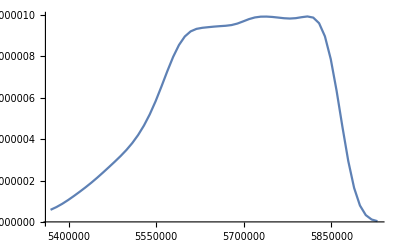

```mathematica
ListLinePlot[Intdat5⟦2⟧]
```

```mathematica
INT6term[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->500000}];
```

```mathematica
Intdat6=Timing[Table[{Eγ,INT6term[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-10*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}]];
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 5.96518×10^-8 and 6.45951×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 7.54076×10^-8 and 7.2792×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 9.40784×10^-8 and 8.25564×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
Intdat6⟦1⟧
```

68.3438

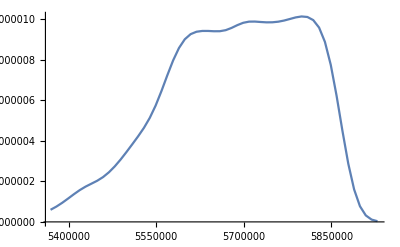

```mathematica
ListLinePlot[Intdat6⟦2⟧]
```

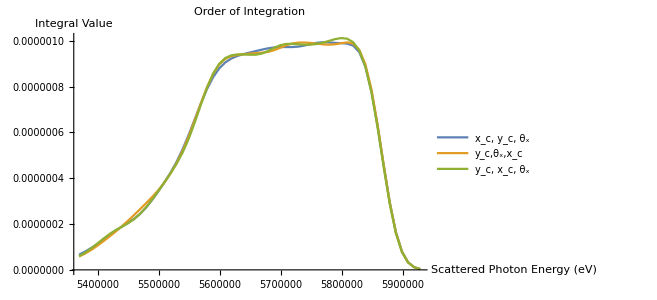

```mathematica
ListLinePlot[{Intdat4⟦2⟧,Intdat5⟦2⟧,Intdat6⟦2⟧},PlotLabel->"Order of Integration",AxesLabel->{"Scattered Photon Energy (eV)","Integral Value"},PlotLegends->Placed[{"x_c, y_c, θ_x","y_c,θ_x,x_c","y_c, x_c, θ_x"},{0.6,0.3}]]
```

## C. Sun Calculation

```mathematica
(*Full Calc + Evaluation*)
dNγdEγ[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_,Eγ_]:=prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]*INTterm[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ];
```

```mathematica
SpecDen=Table[{Eγ*10^-3,dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-15*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,npts/.trialcase}];
```

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 5.72584×10^-13 and 3.93914×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 7.54989×10^-13 and 5.12949×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 9.95945×10^-13 and 6.68154×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

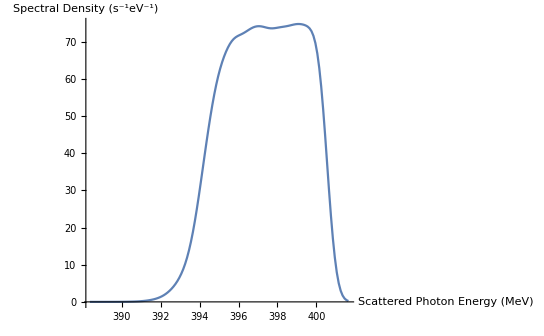

```mathematica
ListLinePlot[SpecDen,AxesLabel->{"Scattered Photon Energy (MeV)","Spectral Density (s^-1eV^-1)"},PlotRange->Full]
```

## Normalised Calculation

```mathematica
NSpecDen=Partition[Riffle[SpecDen⟦All,1⟧,SpecDen⟦All,2⟧/Max[SpecDen]],2];
```

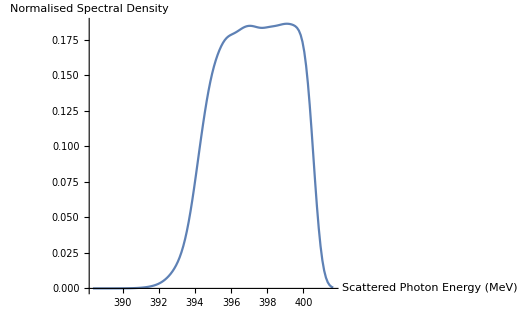

```mathematica
ListLinePlot[NSpecDen,AxesLabel->{"Scattered Photon Energy (MeV)","Normalised Spectral Density"},PlotRange->All]
```

## α Collimation Parameter

```mathematica
α[Ee_,θcol_,ΔEe_]:=(γ[Ee]^2*θcol^2)/(2*Sqrt[2*Log[2]]*2*ΔEe);
```

```mathematica
α[Ee,θcol,ΔEe]/.trialcase
```

5.53394

## Saving Spectrum

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data"];
SpecDen>>"CBETAmatch.txt";
```

## Plotting Cases from File

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data"];
```

```mathematica
(*Importing*)
CBETA150=<<"CBETA150.txt";
CBETA114=<<"CBETA114.txt";
CBETA078=<<"CBETA078.txt";
CBETA042=<<"CBETA042.txt";

CSUNBLACK=<<"CSUNBLACK.txt";
CSUNRED=<<"CSUNRED.txt";
CSUNBLUE=<<"CSUNBLUE.txt";
CSUNPINK=<<"CSUNPINK.txt";
CSUNGREEN=<<"CSUNGREEN.txt";
```

```mathematica
(*CBETA 150MeV 0.5% Bandwidth Case*)
```

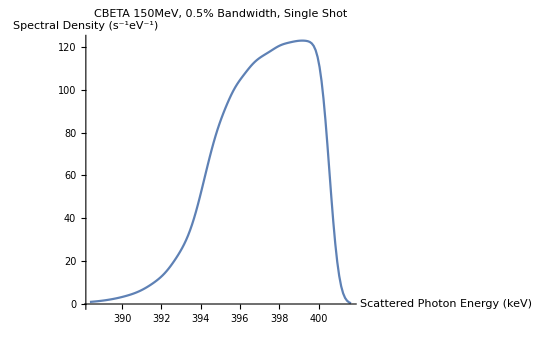

```mathematica
ListLinePlot[CBETA150,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (s^-1eV^-1)"},PlotLabel->"CBETA 150MeV, 0.5% Bandwidth, Single Shot"]
```

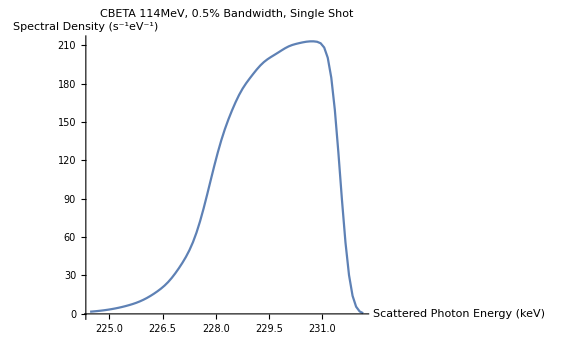

```mathematica
(*CBETA 114MeV 0.5% Bandwidth Case*)
ListLinePlot[CBETA114,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (s^-1eV^-1)"},PlotLabel->"CBETA 114MeV, 0.5% Bandwidth, Single Shot"]
```

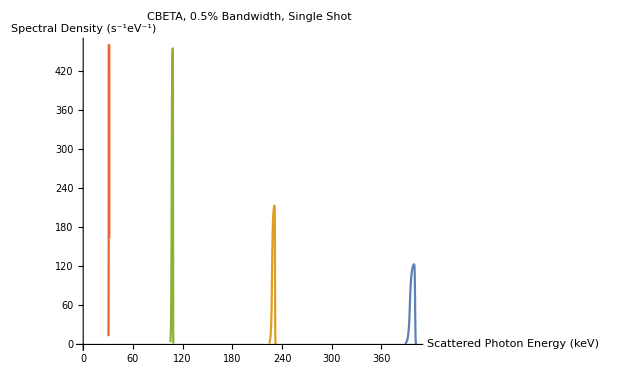

```mathematica
ListLinePlot[{CBETA150,CBETA114,CBETA078,CBETA042},AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (s^-1eV^-1)"},PlotLabel->"CBETA, 0.5% Bandwidth, Single Shot"]
```

The CBETA Spectrum for the 150 MeV, 0.5% bandwidth case. This is for a single electron bunch - laser pulse collision.

```mathematica
ListLinePlot[{CSUNBLACK,CSUNRED,CSUNBLUE,CSUNPINK,CSUNGREEN},Frame->True,FrameLabel->{"Scattered Photon Energy (MeV)","Spectral Density (s^-1eV^-1)"},PlotStyle->{Black,Red,Blue,Purple,Green},PlotLabel->"C. Sun Fig. 3" ,PlotRange->{{5.55,6.05},{0,9*10^9}},PlotLegends->Placed[{"R=14mm, α=5.5","R=12mm, α=4.1","R=10mm, α=2.8","R=8mm, α=1.8","R=4mm, α=0.5"},{0.84,0.7}]]
```

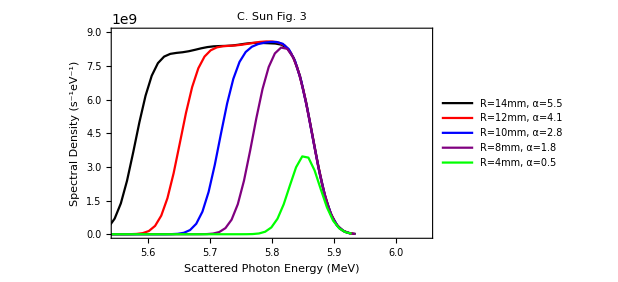
```mathematica
-Graphics--Graphics-
```

# Parameter Investigations

Investigations into individual parameters in the spectral calculation. This looks at the ‘unknown’ parameters (σ_L, β*, Q, E_pulse)  of the C. Sun calculation and the parameters C. Sun plots (ϵ_nx, ΔEe).
Q and E_pulse do exactly as expected and just scale the Spectral Density. There is also a plot to show the difference between square and circular collimation.

## Collimator Shape Investigation

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data"];
```

```mathematica
SquareCASE=<<"SquareCol.txt";
CircCASE=<<"CircCol.txt";
EqualCASE=<<"SquareEqualCircCol.txt";
```

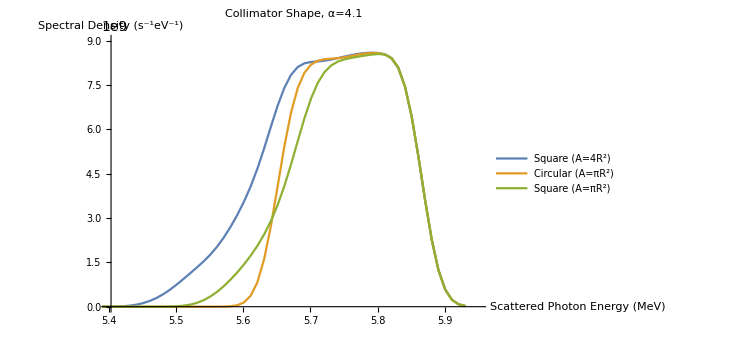

```mathematica
ListLinePlot[{SquareCASE,CircCASE,EqualCASE},PlotLabel->"Collimator Shape, α=4.1",PlotRange->{{5.4,5.95},{0,9*10^9}},AxesLabel->{"Scattered Photon Energy (MeV)","Spectral Density (s^-1eV^-1)"}
,PlotLegends->Placed[{"Square (A=4R^2)","Circular (A=πR^2)","Square (A=πR^2)"},{0.67,0.25}]]
```

## σ_electron vs σ_laser Investigation

```mathematica
(*Storage Ring vs Linac Parameters*)
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data"];
```

```mathematica
StorageRingCASE=<<"StorageRingCase.txt";
LinacCASE=<<"LinacCase.txt";
```

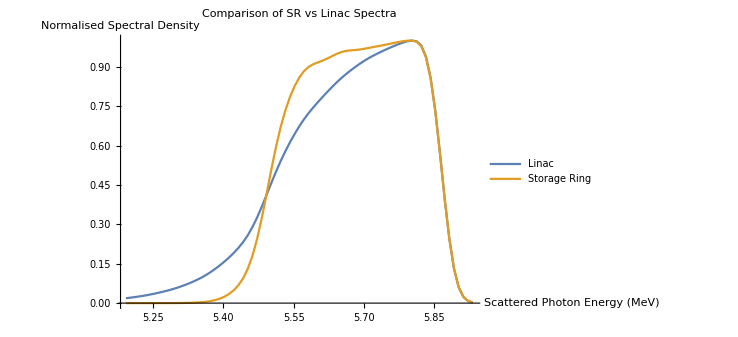

```mathematica
ListLinePlot[{LinacCASE,StorageRingCASE},PlotLabel->"Comparison of SR vs Linac Spectra",AxesLabel->{"Scattered Photon Energy (MeV)","Normalised Spectral Density"},PlotLegends->Placed[{"Linac","Storage Ring"},{0.7,0.3}]]
```

```mathematica
(*Comparison of β^* functions, Subscript[σ, electron]=Subscript[σ, laser] condition held*)
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data/BetaSigLaser"];
Beta001Laser07=<<"beta0.01mlaser0.7um.txt";
Beta01Laser7=<<"beta0.1mlaser7um.txt";
Beta1Laser22=<<"beta1mlaser22um.txt";
Beta2Laser31=<<"beta2mlaser31um.txt";
Beta10Laser70=<<"beta10mlaser70um.txt";
```

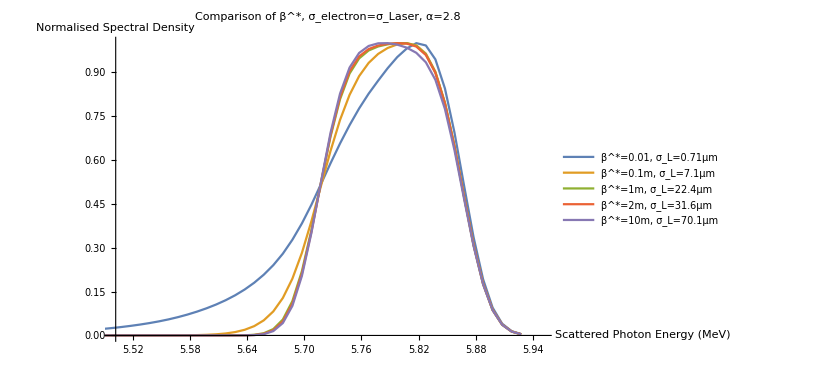

```mathematica
ListLinePlot[{Beta001Laser07,Beta01Laser7,Beta1Laser22,Beta2Laser31,Beta10Laser70},PlotLabel->"Comparison of β^*, σ_electron=σ_Laser, α=2.8",AxesLabel->{"Scattered Photon Energy (MeV)","Normalised Spectral Density"},PlotRange->{{5.5,5.95},{0,1}},PlotLegends->Placed[{"β^*=0.01, σ_L=0.71μm","β^*=0.1m, σ_L=7.1μm","β^*=1m, σ_L=22.4μm","β^*=2m, σ_L=31.6μm","β^*=10m, σ_L=70.1μm"},{0.2,0.7}]]
```

```mathematica
(*Comparison of overfocused, optimised and underfocused using CBETA 150MeV case*)
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data"];
```

```mathematica
underfocus=<<"underfocusedCBETA.txt";
overfocus=<<"overfocusedCBETA.txt";
match=<<"CBETAmatch.txt";
CBETA150=<<"CBETA150.txt";
```

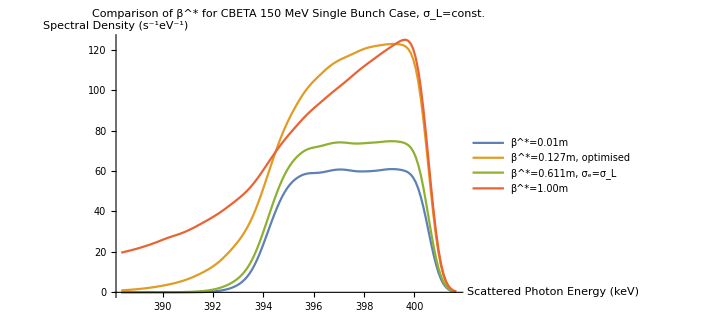

```mathematica
ListLinePlot[{underfocus,CBETA150,match,overfocus},PlotLabel->"Comparison of β^* for CBETA 150 MeV Single Bunch Case, σ_L=const.",AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (s^-1eV^-1)"},PlotLegends->Placed[{"β^*=0.01m","β^*=0.127m, optimised","β^*=0.611m, σ_e=σ_L","β^*=1.00m"},{0.27,0.7}]]
```

## Emittance Investigation (Normalised Spectra)

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data/Emittance"];
```

```mathematica
ϵxBLACK=<<"emit_BLACK.txt";
ϵxRED=<<"emit_RED.txt";
ϵxBLUE=<<"emit_BLUE.txt";
ϵxPINK=<<"emit_PINK.txt";
```

```mathematica
ListLinePlot[{ϵxBLACK,ϵxRED,ϵxBLUE,ϵxPINK},PlotLabel->"Emittance  Effect on Normalised Spectra",Frame->True,FrameLabel->{"Scattered Photon Energy (MeV)","Normalised Spectral Density"},PlotStyle->{Black,Red,Blue,Pink},PlotLegends->Placed[{"ϵ_x= 0.5nm rad","ϵ_x= 10nm rad","ϵx= 100nm rad","ϵ_x= 500nm rad"},{0.7,0.3}]]
```

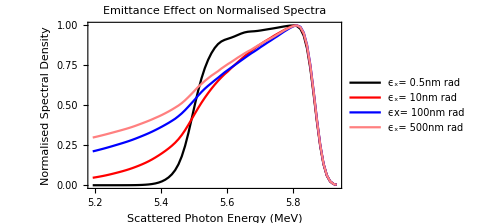
```mathematica
-Graphics--Graphics-
```

[15/07/2020] These plots show that emittance isn’t behaving correctly in the spectral calculation in comparison to Fig. 4a of C. Sun’s paper. The tails contain more intensity and don’t increase in intensity at high emittance. The ‘bulk’ of the distribution also doesn’t always increase in slope with increasing emittance as expected in Fig. 4. However, this could possibly result from an incorrect choice of β^*.  Storage ring parameters produce a better looking plot than the linac/ERL parameters.

## Energy Spread Investigation (Normalised Spectra)

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data/EnergySpread"];
```

```mathematica
SPREADBLACK=<<"SPREAD_BLACK.txt";
SPREADRED=<<"SPREAD_RED.txt";
SPREADBLUE=<<"SPREAD_BLUE.txt";
SPREADPINK=<<"SPREAD_PINK.txt";
```

```mathematica
ListLinePlot[{SPREADBLACK,SPREADRED,SPREADBLUE,SPREADPINK},PlotLabel->"Emittance  Effect on Normalised Spectra",Frame->True,FrameLabel->{"Scattered Photon Energy (MeV)","Normalised Spectral Density"},PlotStyle->{Black,Red,Blue,Pink},PlotRange->{{5.0,6.1},{0,1}},PlotLegends->Placed[{"ΔE_e/E_e=5*10^-4","ΔE_e/E_e=2*10^-3","ΔE_e/E_e=4*10^-3","ΔE_e/E_e=8*10^-3"},{0.2,0.7}]]
```

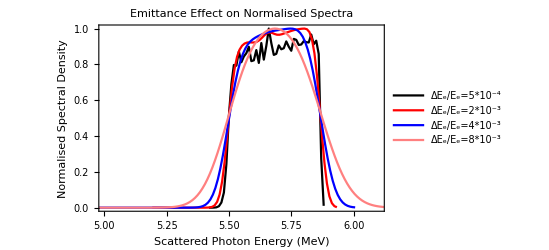
```mathematica
-Graphics--Graphics-
```

[15/07/2020] The Plot shows the general trend that is expected from the energy spread effect on the spectra. However, this is hard to gauge since the integration has not been calculated to be a smooth curve for both the red and black curves. This suggests some more work is necessary on the integration methods.